```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
list = Drop[ReadList["pdf_home.txt",{Number,Number,Number,Number}],-30];
win = Drop[list,0,-2];
tie = Drop[list,0,{2,4,2}];
loss = Drop[list,0,{2,3}] ;
```

SHIFT FUNCTIONS TO THE RIGHT BY HALF A BIN, SINCE THE X-COORDINATES HERE ARE LEFT BIN BORDERS!

1/(0.993745588217890352+1.20447136550852012 ⅇ^(-1.16527348239199668 x))

0.411372791788055856 ⅇ^(-0.827794997859682452 x)

0.179762416000732405 ⅇ^(-0.97526621267591847 x)

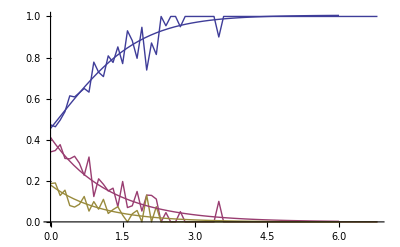

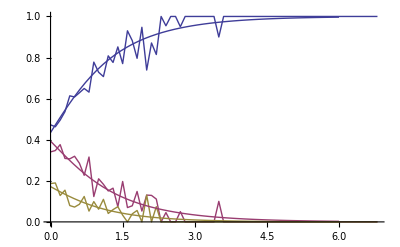

```mathematica
modell = d Exp[e x];
modelw = 1/(a + b Exp[c x]);
modelt = f Exp[g x];
fitw=modelw/.FindFit[win,modelw,{a,b,c},x]
fitt=modelt/.FindFit[tie,modelt,{f,g},x]
fitl=modell/.FindFit[loss,modell,{d,e},x]
Show[ListPlot[{win,tie,loss},Joined->True],Plot[{fitw,fitt,fitl},{x,0,6}]]
Show[ListPlot[{win,tie,loss},Joined->True],Plot[{fitw/(fitw+fitt+fitl),fitt/(fitw+fitt+fitl),fitl/(fitw+fitt+fitl)},{x,0,6}]]
```

```mathematica
list = Drop[ReadList["pdf_nohome.txt",{Number,Number,Number,Number}],-30];
win = Drop[list,0,-2];
tie = Drop[list,0,{2,4,2}];
loss = Drop[list,0,{2,3}] ;
```

SHIFT FUNCTIONS TO THE RIGHT BY HALF A BIN, SINCE THE X-COORDINATES HERE ARE LEFT BIN BORDERS!

1/(0.999381312615316369+1.60047731001837545 ⅇ^(-1.06709836157930476 x))

0.363029702153055662 ⅇ^(-0.63217499754200404 x)

0.326256890083060776 ⅇ^(-0.906662594450005946 x)

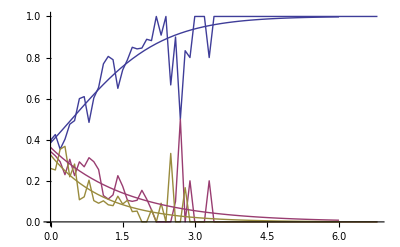

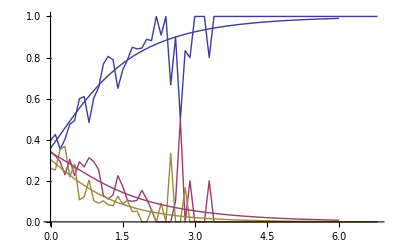

```mathematica
modell = d Exp[e x];
modelw = 1/(a + b Exp[c x]);
modelt = f Exp[g x];
fitw=modelw/.FindFit[win,modelw,{a,b,c},x]
fitt=modelt/.FindFit[tie,modelt,{f,g},x]
fitl=modell/.FindFit[loss,modell,{d,e},x]
Show[ListPlot[{win,tie,loss},Joined->True],Plot[{fitw,fitt,fitl},{x,0,6}]]
Show[ListPlot[{win,tie,loss},Joined->True],Plot[{fitw/(fitw+fitt+fitl),fitt/(fitw+fitt+fitl),fitl/(fitw+fitt+fitl)},{x,0,6}]]
```

```mathematica
list = Drop[ReadList["pdf_ahome.txt",{Number,Number,Number,Number}],-30];
win = Drop[list,0,-2];
tie = Drop[list,0,{2,4,2}];
loss = Drop[list,0,{2,3}] ;
```

SHIFT FUNCTIONS TO THE RIGHT BY HALF A BIN, SINCE THE X-COORDINATES HERE ARE LEFT BIN BORDERS!

1/(0.974568627036329208+2.65013610774447005 ⅇ^(-0.835449469892954494 x))

0.398367959209470331 ⅇ^(-0.458448718924871196 x)

0.456455748206617582 ⅇ^(-0.69127538370508761 x)

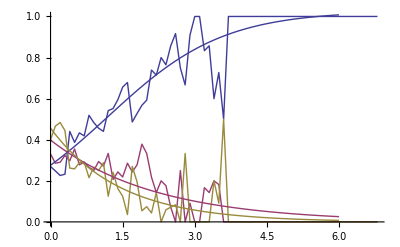

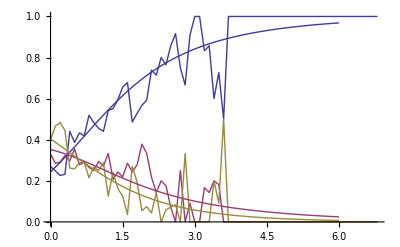

```mathematica
modell = d Exp[e x];
modelw = 1/(a + b Exp[c x]);
modelt = f Exp[g x];
fitw=modelw/.FindFit[win,modelw,{a,b,c},x]
fitt=modelt/.FindFit[tie,modelt,{f,g},x]
fitl=modell/.FindFit[loss,modell,{d,e},x]
Show[ListPlot[{win,tie,loss},Joined->True],Plot[{fitw,fitt,fitl},{x,0,6}]]
Show[ListPlot[{win,tie,loss},Joined->True],Plot[{fitw/(fitw+fitt+fitl),fitt/(fitw+fitt+fitl),fitl/(fitw+fitt+fitl)},{x,0,6}]]
```